```mathematica
data = 
{{0.27931,15.76,1.07424,3.87},{0.837931,42.49,2.46665,4.93},{1.39655,70.03,3.27774,10.44},{1.95517,105.83,3.68792,4.},{2.51379,118.54,3.84641,4.},{3.07241,126.9,3.88202,3.08},{3.63103,140.32,4.1325,4.},{4.18966,144.27,5.44853,4.02},{4.74828,155.65,7.01228,5.36},{5.3069,149.54,8.38873,5.41},{5.86552,150.65,9.76333,7.06},{6.42414,155.02,11.1443,4.66},{6.98276,166.94,12.5646,6.},{7.54138,167.37,14.0251,2.63},{8.1,163.17,15.4947,3.32},{8.65862,164.38,16.9319,2.43},{9.21724,160.2,18.5489,5.7},{9.77586,164.47,20.3382,3.79},{10.3345,172.81,22.3449,8.51},{10.8931,165.95,24.5708,2.},{15.3621,163.72,52.6146,10.79},{15.9207,173.94,56.4422,2.},{18.6207,176.44,67.7037,2.8},{20.6897,182.08,68.486,2.31},{22.7586,184.16,66.5516,2.07},{24.8276,183.3,62.8426,2.05}};

RC=Table[{data[[i,1]],data[[i,2]]},{i,1,26}];
Rgas=Table[{data[[i,1]],data[[i,3]]},{i,1,26}];
Erro = Table[data[[i,4]],{i,1,26}];
TableForm[data,TableHeadings->{{"ESO 287-G13"},{"Raio","Vtotal","Vgas","Erro"}}]
```

| Raio | Vtotal | Vgas | Erro
ESO 287-G13 | 0.27931 | 15.76 | 1.07424 | 3.87
 | 0.837931 | 42.49 | 2.46665 | 4.93
 | 1.39655 | 70.03 | 3.27774 | 10.44
 | 1.95517 | 105.83 | 3.68792 | 4.
 | 2.51379 | 118.54 | 3.84641 | 4.
 | 3.07241 | 126.9 | 3.88202 | 3.08
 | 3.63103 | 140.32 | 4.1325 | 4.
 | 4.18966 | 144.27 | 5.44853 | 4.02
 | 4.74828 | 155.65 | 7.01228 | 5.36
 | 5.3069 | 149.54 | 8.38873 | 5.41
 | 5.86552 | 150.65 | 9.76333 | 7.06
 | 6.42414 | 155.02 | 11.1443 | 4.66
 | 6.98276 | 166.94 | 12.5646 | 6.
 | 7.54138 | 167.37 | 14.0251 | 2.63
 | 8.1 | 163.17 | 15.4947 | 3.32
 | 8.65862 | 164.38 | 16.9319 | 2.43
 | 9.21724 | 160.2 | 18.5489 | 5.7
 | 9.77586 | 164.47 | 20.3382 | 3.79
 | 10.3345 | 172.81 | 22.3449 | 8.51
 | 10.8931 | 165.95 | 24.5708 | 2.
 | 15.3621 | 163.72 | 52.6146 | 10.79
 | 15.9207 | 173.94 | 56.4422 | 2.
 | 18.6207 | 176.44 | 67.7037 | 2.8
 | 20.6897 | 182.08 | 68.486 | 2.31
 | 22.7586 | 184.16 | 66.5516 | 2.07
 | 24.8276 | 183.3 | 62.8426 | 2.05

```mathematica
Igas = Interpolation[Rgas]
```

InterpolatingFunction[{{0.27931, 24.8276}}, <>]

```mathematica
Vd[r_,M_]:=1/(2 Rd)(G (M *10^9) (r/Rd)^2) (BesselI[0,r/(2 Rd)] BesselK[0,r/(2 Rd)]-BesselI[1,r/(2 Rd)] BesselK[1,r/(2 Rd)]);
Vme[r_,R_,P_]:=1/r 6.4 G ((P *10^7) R^3) (1/2 Log[(r/R)^2+1]+Log[r/R+1]-ArcTan[r/R]);
Vt[r_,M_,R_,P_]:=Sqrt[Vd[r,M]+Vme[r,R,P]+Igas[r]^2];
G:=4.302/10^6;
Rd:=3.3;
```

```mathematica
Ajuste= NonlinearModelFit[RC,Vt[r,M,R,P],{{R,1,50},{M,1,30},{P,4,10}},r, Weights->1/Erro^2]
Ajuste["ParameterTable"]
```

FittedModel[√(2726.76 r^2 (BesselI[0,0.151515 r] BesselK[0,0.151515 r]-BesselI[1,0.151515 r] BesselK[1,«1»])+«1»+«1»)]

| Estimate | Standard Error | t-Statistic | P-Value
R | 28.4899 | 5.9341 | 4.80105 | 0.0000764508
M | 45.5563 | 1.26035 | 36.1458 | 9.06197×10^-22
P | 0.430196 | 0.0775027 | 5.55072 | 0.0000120272

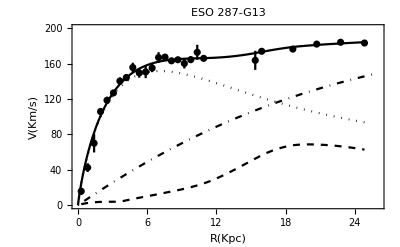

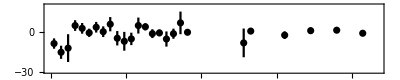

```mathematica
Needs["ErrorBarPlots`"];

RCtotal = Plot[Ajuste[r],{r,0,24.82}, PlotStyle->Black, PlotRange->{{0,26},{0,183.3}}];Vstars = Plot[Sqrt[Vd[r,M]]/.M->45.56,{r,0,24.83}, PlotStyle->{Black,Dotted}];
Vhalo = Plot[Sqrt[Vme[r,R,P]]/.{R->28.48,P->0.43},{r,0,26},PlotStyle->{Black,DotDashed}];
Gas =Plot[Igas[x],{x,0.27931,24.8276},PlotStyle->{Black,Dashed},AxesLabel->{"R(Kpc)","V(Km/s)"}];
VRC = ErrorListPlot[{Table[{RC[[i]],ErrorBar[Erro[[i]]]},{i,26}]},PlotStyle->Black,MeshStyle->PointSize[Large]];
RCurve = Plot[Vt[r,M,R,P]/.{M->45.56,R->28.48,P->0.43},{r,0,24.8},PlotStyle->Black,PlotRange->{{0,26},{0,200}}];

Show[RCurve,VRC,Vstars,Vhalo,Gas, Frame->True,PlotRange->{{0,26},{0,200}},PlotLabel->"ESO 287-G13",FrameLabel->{"R(Kpc)","V(Km/s)"}]
ErrorListPlot[{Table[{Table[{data[[i,1]],Ajuste["FitResiduals"][[i]]},{i,26}][[i]],ErrorBar[Erro[[i]]]},{i,26}]}, PlotStyle->Black, MeshStyle->PointSize[Large], PlotRange->{{0,26},{-30,20}},Frame->True, AspectRatio->0.2]
```